Wolfram Online Mini Campus. Part 23

Instagram Posts
Pinterest Posts
"Translation" of  📑  SageMath Online Mini Campus. Part 23
http://www.wolfram.com/broadcast/video.php?c=460&v=2672
https://blog.stephenwolfram.com/2019/04/version-12-launches-today-big-jump-for-wolfram-language-and-mathematica/
https://sparse.tamu.edu/

Functions as Creativity Expression

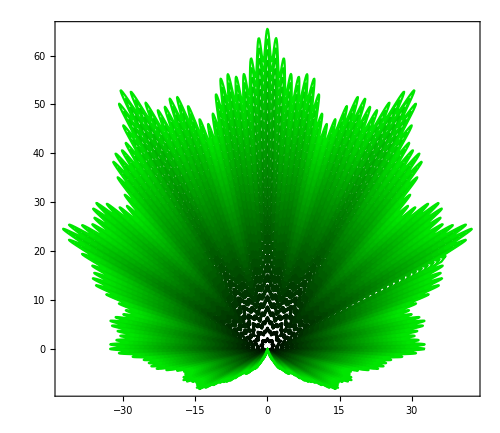

```mathematica
F1[t_]:=(9+.9Cos[12t])(1+.05Cos[36t]);
F2[t_]:=(1+.05Cos[216t])(1+Sin[t])
Show[Table[PolarPlot[i*F1[t]*F2[t],{t,0,2Pi},
PlotStyle->Darker[Green,1-.3i]],{i,0,3,.1}],
ImageSize->500,Frame->True,Axes->False]
```

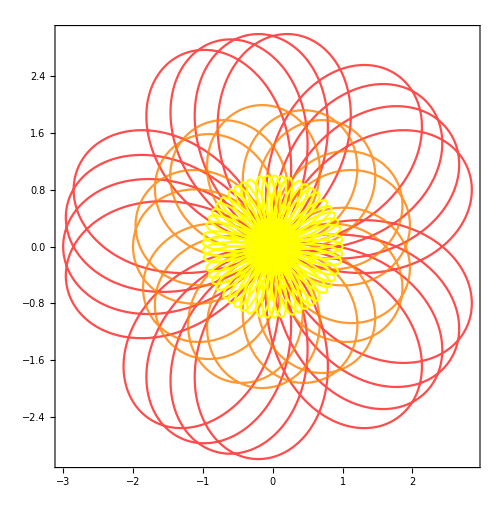

```mathematica
Show[PolarPlot[3Sin[1.7t],{t,0,11.7Pi},
PlotStyle->{Red,Opacity[.7]}],
PolarPlot[2Sin[1.3t],{t,0,13Pi},
PlotStyle->{Orange,Opacity[.8]}],
PolarPlot[Sin[5.9t],{t,0,9Pi},PlotStyle->Yellow],
ImageSize->500,Frame->True,Axes->False]
```

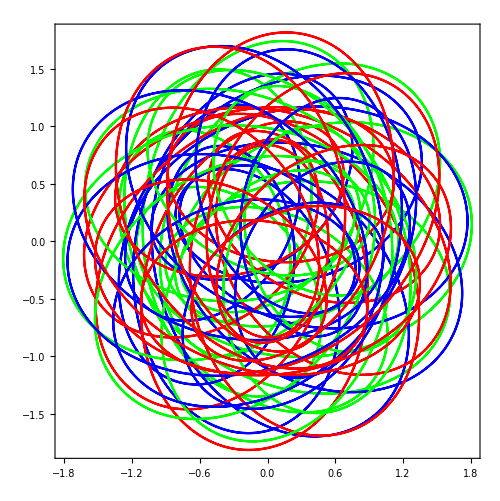

```mathematica
FXY=Function[{t,i,n},
{Cos[16t+i*Pi/n]+Cos[6t+i*Pi/n]/2+Sin[10t+i*Pi/n]/3,
Sin[16t+i*Pi/n]+Sin[6t+i*Pi/n]/2+Cos[10t+i*Pi/n]/3}];
Show[Table[ParametricPlot[FXY[t,i,3],{t,0,2Pi},
PlotStyle->Hue[i/3]],{i,6}],
PlotRange->All,ImageSize->500,Frame->True,Axes->False]
```

```mathematica
POPMN[m_,n_,k_,θ_]:=Cos[m*θ]+Cos[n*θ]+k;
PAPMN=Function[{m,n,k,t},
{(Cos[m*t]+Cos[n*t]+k+1)Cos[t],
(Cos[m*t]+Cos[n*t]+k+1)Sin[t]}];
CPMN=Function[{m,n,k,x,y},
x^2+y^2-(Cos[m*ArcTan[y/x]]+Cos[n*ArcTan[y/x]]+k+2)^2];
S3P=Function[{m,n,k,c1,c2,c3},
Show[PolarPlot[POPMN[m,n,k,θ],{θ,0,2Pi},
PlotStyle->ColorData[c1][1-.1k]],
ParametricPlot[PAPMN[m,n,k,t],{t,0,2Pi+.1},
PlotStyle->ColorData[c2][1-.3k]],
ContourPlot[CPMN[m,n,k,x,y]==0,{x,-6,6},{y,-6,6},
ContourStyle->ColorData[c3][1-.5k]],
Axes->False,ImageSize->500,Frame->True]];
S3P[24,12,2,"RoseColors","AvocadoColors","NeonColors"]
```

-Graphics-

```mathematica
z[n_]:=Exp[I*Pi*n*2^0.3]; L={{0,0}};
Do[L=Append[L,{Re[L[[i,1]]+I*L[[i,2]]+z[i]],
Im[L[[i,1]]+I*L[[i,2]]+z[i]]}],{i,250}];
Graphics[Table[{Hue[i/250],
Line[{L[[i]],L[[i+1]]}]},{i,250}],
ImageSize->500,Background->RGBColor["silver"]]
```

-Graphics-

Exercises with Functions

```mathematica
Pl[x1_,x2_]:=Plot[{-Log[x],-Log[x]*x},
{x,x1,x2},PlotStyle->{Blue,Magenta}];
Va[x_]:=Graphics[{Blue,Text[Style[N[-Log[x]*x],20],
{x+.1,-Log[x]+.1}],Opacity[.3],Polygon[{{0,0},
{x,0},{x,-Log[x]},{0,-Log[x]}}]}];
xmax=Solve[D[-Log[x]*x,x]==0,x][[1,1,2]];
Vmax=Graphics[{Red,Text[Style[-Log[xmax]*xmax,30],
{xmax+.05,-Log[xmax]+.1}],Text[Style["*",30],
{xmax,-Log[xmax]*xmax-.1}],Opacity[.5],
Polygon[{{0,0},{xmax,0},
{xmax,-Log[xmax]},{0,-Log[xmax]}}]}];
Show[Pl[0,1.1],Vmax,Va[.15],Va[.65],
ImageSize->600,GridLines->Automatic]
```

-Graphics-

3D Graphics as Creativity Expression

```mathematica
MenuView[PolyhedronData["Archimedean"][[1;;13]]]
```

```mathematica
PolyhedronData["Properties"]
```

{AlternateNames,AlternateStandardNames,Amphichiral,Antiprism,Archimedean,ArchimedeanDual,BoundaryMeshRegion,Centroid,Chiral,Circumcenter,Circumradius,Circumsphere,Classes,Compound,Concave,Convex,DefaultOrientation,Deltahedron,DihedralAngles,Dipyramid,Dual,DualCompound,EdgeCount,EdgeIndices,EdgeLengths,Entity,Equilateral,FaceCount,FaceIndices,GeneralizedDiameter,Graphics3D,GraphicsComplex,Image,ImplicitRegion,Incenter,InertiaTensor,Information,Inradius,Insphere,Isohedron,Johnson,KeplerPoinsot,Lines,MeshRegion,Midcenter,Midradius,Midsphere,MultipieceNetCoordinates,MultipieceNetFaceIndices,MultipieceNetImage,Name,Net,NetCount,NotationRules,Orientations,Platonic,PlatonicDual,Points,Polygons,Polyhedron,PolyhedronCompoundComponents,Prism,Pyramid,Quasiregular,Region,RegionFunction,Rhombohedron,Rigid,SchlaefliSymbol,SelfDual,Shaky,Skeleton,SpaceFilling,StandardName,StandardNames,Stellation,StellationCount,SurfaceArea,SymmetryGroup,SymmetryGroupString,Uniform,UniformDual,VertexCoordinates,VertexCount,VertexSubsetHulls,Volume,WythoffSymbol,Zonohedron}

```mathematica
Multicolumn[ColorData["Crayola",
"ColorRules"][[11;;80]],5]
```

BlizzardBlue→RGBColor[0.6745098039215687, 0.8980392156862745, 0.9333333333333333] | CarnationPink→RGBColor[1.0, 0.6666666666666666, 0.8] | Fuchsia→RGBColor[0.7647058823529411, 0.39215686274509803, 0.7725490196078432] | LaserLemon→RGBColor[0.996078431372549, 0.996078431372549, 0.13333333333333333] | MountainMeadow→RGBColor[0.18823529411764706, 0.7294117647058823, 0.5607843137254902]
Blue→RGBColor[0.12156862745098039, 0.4588235294117647, 0.996078431372549] | Cerise→RGBColor[0.8666666666666667, 0.26666666666666666, 0.5725490196078431] | FuzzyWuzzy→RGBColor[0.8, 0.4, 0.4] | Lavender→RGBColor[0.9882352941176471, 0.7058823529411765, 0.8352941176470589] | Mulberry→RGBColor[0.7725490196078432, 0.29411764705882354, 0.5490196078431373]
BlueBell→RGBColor[0.6352941176470588, 0.6352941176470588, 0.8156862745098039] | Cerulean→RGBColor[0.11372549019607843, 0.6745098039215687, 0.8392156862745098] | Gold→RGBColor[0.9058823529411765, 0.7764705882352941, 0.592156862745098] | LemonYellow→RGBColor[1.0, 0.9568627450980393, 0.30980392156862746] | NavyBlue→RGBColor[0.09803921568627451, 0.4549019607843137, 0.8235294117647058]
BlueGray→RGBColor[0.4, 0.6, 0.8] | Chestnut→RGBColor[0.7372549019607844, 0.36470588235294116, 0.34509803921568627] | Goldenrod→RGBColor[0.9882352941176471, 0.8509803921568627, 0.4588235294117647] | MacaroniandCheese→RGBColor[1.0, 0.7411764705882353, 0.5333333333333333] | NeonCarrot→RGBColor[1.0, 0.6392156862745098, 0.2627450980392157]
BlueGreen→RGBColor[0.050980392156862744, 0.596078431372549, 0.7294117647058823] | Copper→RGBColor[0.8666666666666667, 0.5803921568627451, 0.4588235294117647] | GrannySmithApple→RGBColor[0.6588235294117647, 0.8941176470588236, 0.6274509803921569] | Magenta→RGBColor[0.9647058823529412, 0.39215686274509803, 0.6862745098039216] | OliveGreen→RGBColor[0.7294117647058823, 0.7215686274509804, 0.4235294117647059]
BlueViolet→RGBColor[0.45098039215686275, 0.4, 0.7411764705882353] | Cornflower→RGBColor[0.6039215686274509, 0.807843137254902, 0.9215686274509803] | Gray→RGBColor[0.5843137254901961, 0.5686274509803921, 0.5490196078431373] | MagicMint→RGBColor[0.6666666666666666, 0.9411764705882353, 0.8196078431372549] | Orange→RGBColor[1.0, 0.4588235294117647, 0.2196078431372549]
Blush→RGBColor[0.8705882352941177, 0.36470588235294116, 0.5137254901960784] | CottonCandy→RGBColor[1.0, 0.7372549019607844, 0.8509803921568627] | Green→RGBColor[0.10980392156862745, 0.6745098039215687, 0.47058823529411764] | Mahogany→RGBColor[0.803921568627451, 0.2901960784313726, 0.2980392156862745] | OrangeRed→RGBColor[1.0, 0.16862745098039217, 0.16862745098039217]
BrickRed→RGBColor[0.796078431372549, 0.2549019607843137, 0.32941176470588235] | Dandelion→RGBColor[0.9921568627450981, 0.8588235294117647, 0.42745098039215684] | GreenBlue→RGBColor[0.06666666666666667, 0.39215686274509803, 0.7058823529411765] | Maize→RGBColor[0.9294117647058824, 0.8196078431372549, 0.611764705882353] | OrangeYellow→RGBColor[0.9725490196078431, 0.8352941176470589, 0.40784313725490196]
Brown→RGBColor[0.7058823529411765, 0.403921568627451, 0.30196078431372547] | Denim→RGBColor[0.16862745098039217, 0.4235294117647059, 0.7686274509803922] | GreenYellow→RGBColor[0.9411764705882353, 0.9098039215686274, 0.5686274509803921] | Manatee→RGBColor[0.592156862745098, 0.6039215686274509, 0.6666666666666666] | Orchid→RGBColor[0.9019607843137255, 0.6588235294117647, 0.8431372549019608]
BurntOrange→RGBColor[1.0, 0.4980392156862745, 0.28627450980392155] | DesertSand→RGBColor[0.9372549019607843, 0.803921568627451, 0.7215686274509804] | HotMagenta→RGBColor[0.9725490196078431, 0.09019607843137255, 0.24313725490196078] | MangoTango→RGBColor[1.0, 0.5098039215686274, 0.2627450980392157] | OuterSpace→RGBColor[0.2549019607843137, 0.2901960784313726, 0.2980392156862745]
BurntSienna→RGBColor[0.9176470588235294, 0.49411764705882355, 0.36470588235294116] | Eggplant→RGBColor[0.43137254901960786, 0.3176470588235294, 0.3764705882352941] | Inchworm→RGBColor[0.6980392156862745, 0.9254901960784314, 0.36470588235294116] | Maroon→RGBColor[0.7843137254901961, 0.2196078431372549, 0.35294117647058826] | OutrageousOrange→RGBColor[1.0, 0.43137254901960786, 0.2901960784313726]
CadetBlue→RGBColor[0.6901960784313725, 0.7176470588235294, 0.7764705882352941] | ElectricLime→RGBColor[0.807843137254902, 1.0, 0.11372549019607843] | Indigo→RGBColor[0.36470588235294116, 0.4627450980392157, 0.796078431372549] | Mauvelous→RGBColor[0.9372549019607843, 0.596078431372549, 0.6666666666666666] | PacificBlue→RGBColor[0.10980392156862745, 0.6627450980392157, 0.788235294117647]
Canary→RGBColor[1.0, 1.0, 0.6] | Fern→RGBColor[0.44313725490196076, 0.7372549019607844, 0.47058823529411764] | JazzberryJam→RGBColor[0.792156862745098, 0.21568627450980393, 0.403921568627451] | Melon→RGBColor[0.9921568627450981, 0.7372549019607844, 0.7058823529411765] | Peach→RGBColor[1.0, 0.8117647058823529, 0.6705882352941176]
CaribbeanGreen→RGBColor[0.10980392156862745, 0.8274509803921568, 0.6352941176470588] | ForestGreen→RGBColor[0.42745098039215684, 0.6823529411764706, 0.5058823529411764] | JungleGreen→RGBColor[0.23137254901960785, 0.6901960784313725, 0.5607843137254902] | MidnightBlue→RGBColor[0.10196078431372549, 0.2823529411764706, 0.4627450980392157] | Periwinkle→RGBColor[0.7725490196078432, 0.8156862745098039, 0.9019607843137255]

```mathematica
PDG[p_]:=Graphics3D[{Opacity[.3],
Tube[PolyhedronData[p,"Edges","Coordinates"],.05],
EdgeForm[Transparent],FaceForm[Opacity[.7],White],
Transpose[{ColorData["Crayola",
"ColorList"][[11;;10+Length[#]]],
#}]}]&@PolyhedronData[p,"Polygons"];
PDT[p_]:=Graphics3D[MapIndexed[Style[Text[ColorData["Crayola"][[3,
1,10+#2[[1]]]],#1],15]&,Mean/@(PolyhedronData[p,
"VertexCoordinates"][[#]]&/@PolyhedronData[p,"FaceIndices"])]];
Show[PDG[PolyhedronData["Archimedean"][[11]]],
PDT[PolyhedronData["Archimedean"][[11]]],
 Boxed->False,ImageSize->700,ViewPoint->{-3,-1,3.5}]
```

-Graphics3D-

```mathematica
RR=RandomReal[{-1.5,1.5},{101,3}]; SeedRandom[11];
RW=RandomFunction[BrownianBridgeProcess[{0,0},{1,1}],
{0, 1,.01},3]["ValueList"];
Graphics3D[Table[{Style[Tube[(Transpose@RW)[[i;;i+1]],.03],
ColorData["BrightBands"][.01i]],Style[Tube[RR[[i;;i+1]],.02],
ColorData["DarkBands"][.01i],Opacity[.2]]},{i,100}]]
```

-Graphics3D-

Exercises with HTML & D3.js Objects

```mathematica
EmbeddedHTML["<style>svg {background-color:slategray;} text {fill:#fff; font-size:135%;} 
.point {stroke:#fff; stroke-width:1;}             
.grid line, .grid path {stroke:#fff; stroke-opacity:0.9; shape-rendering:crispEdges;}</style>
<body><script src='https://d3js.org/d3.v4.min.js'></script><script>
var n=255,m=35,margin={top:m,right:m,bottom:m,left:m},
    width=500-margin.left-margin.right,height=500-margin.top-margin.bottom; 
var xScale=d3.scaleLinear().domain([-1,1]).range([0,width]); 
var yScale=d3.scaleLinear().domain([-1,1]).range([height,0]);
function make_x_gridlines() {return d3.axisBottom(xScale).ticks(11)};
function make_y_gridlines() {return d3.axisLeft(yScale).ticks(11)};
var pointColor=d3.scaleSequential().domain([0,n]).interpolator(d3.interpolateCool);            
var data=d3.range(0,n).map(function(i){return {'x':Math.sin(0.05*i),'y':Math.sin(0.125*i)}})
var svg=d3.select('body').append('svg')
          .attr('width',width+margin.left+margin.right).attr('height',height+margin.top+margin.bottom)
          .append('g').attr('transform','translate('+margin.left+','+margin.top+')');
svg.append('g').attr('class','x axis').call(d3.axisBottom(xScale).tickSize(0.5))
               .attr('transform','translate(0,'+height+')'); 
svg.append('g').attr('class','y axis').call(d3.axisLeft(yScale).tickSize(0.5));    
svg.append('g').attr('class','grid').attr('transform','translate(0,'+height+')')
               .call(make_x_gridlines().tickSize(-height).tickFormat(''));
svg.append('g').attr('class','grid').call(make_y_gridlines().tickSize(-width).tickFormat(''));
svg.selectAll('.point').data(data).enter().append('circle').attr('class','point')
    .attr('fill',function(d,i){return pointColor(i)}).attr('r',3.5)
    .attr('cx',function(d) {return xScale(d.x)}).attr('cy',function(d) {return yScale(d.y)});
</script>",ImageSize->{550,550}]
```

Null<style>svg {background-color:slategr…(d) {return yScale(d.y)});
</script><style>svg {background-color:slategray;} text {fill:#fff; font-size:135%;} 
.point {stroke:#fff; stroke-width:1;}             
.grid line, .grid path {stroke:#fff; stroke-opacity:0.9; shape-rendering:crispEdges;}</style>
<body><script src='https://d3js.org/d3.v4.min.js'></script><script>
var n=255,m=35,margin={top:m,right:m,bottom:m,left:m},
    width=500-margin.left-margin.right,height=500-margin.top-margin.bottom; 
var xScale=d3.scaleLinear().domain([-1,1]).range([0,width]); 
var yScale=d3.scaleLinear().domain([-1,1]).range([height,0]);
function make_x_gridlines() {return d3.axisBottom(xScale).ticks(11)};
function make_y_gridlines() {return d3.axisLeft(yScale).ticks(11)};
var pointColor=d3.scaleSequential().domain([0,n]).interpolator(d3.interpolateCool);            
var data=d3.range(0,n).map(function(i){return {'x':Math.sin(0.05*i),'y':Math.sin(0.125*i)}})
var svg=d3.select('body').append('svg')
          .attr('width',width+margin.left+margin.right).attr('height',height+margin.top+margin.bottom)
          .append('g').attr('transform','translate('+margin.left+','+margin.top+')');
svg.append('g').attr('class','x axis').call(d3.axisBottom(xScale).tickSize(0.5))
               .attr('transform','translate(0,'+height+')'); 
svg.append('g').attr('class','y axis').call(d3.axisLeft(yScale).tickSize(0.5));    
svg.append('g').attr('class','grid').attr('transform','translate(0,'+height+')')
               .call(make_x_gridlines().tickSize(-height).tickFormat(''));
svg.append('g').attr('class','grid').call(make_y_gridlines().tickSize(-width).tickFormat(''));
svg.selectAll('.point').data(data).enter().append('circle').attr('class','point')
    .attr('fill',function(d,i){return pointColor(i)}).attr('r',3.5)
    .attr('cx',function(d) {return xScale(d.x)}).attr('cy',function(d) {return yScale(d.y)});
</script>

```mathematica
EmbeddedHTML["<style>svg {background-color:slategray;} .point1, .point2 {stroke:#fff; stroke-width:1;}
.grid1 line, .grid1 path {stroke:#fff; stroke-opacity:0.9; shape-rendering:crispEdges;}</style>
<body><script src='https://d3js.org/d3.v5.min.js'></script><script>
var n=630, m0=35, m={top:m0,right:m0,bottom:m0,left:m0}, w=500-m.left-m.right, h=500-m.top-m.bottom; 
var xScale=d3.scaleLinear().domain([-3,3]).range([0,w]); var yScale=d3.scaleLinear().domain([-3,3]).range([h,0]);
function make_x_gridlines() {return d3.axisBottom(xScale).ticks(11)}; 
function make_y_gridlines() {return d3.axisLeft(yScale).ticks(11)};
var svg=d3.select('body').append('svg').attr('width',w+m.left+m.right).attr('height',h+m.top+m.bottom)
                        .append('g').attr('transform','translate('+m.left+','+m.top+')');
svg.append('g').attr('class','grid1').attr('transform','translate(0,'+h+')')
              .call(make_x_gridlines().tickSize(-h).tickFormat(''));
svg.append('g').attr('class','grid1').call(make_y_gridlines().tickSize(-w).tickFormat(''));
var data1=d3.range(0,n).map(function(i){return {'x':(Math.cos(0.12*i)+1)*Math.cos(0.01*i),
                                         'y':(Math.cos(0.12*i)+1)*Math.sin(0.01*i)}});
var data2=d3.range(0,n).map(function(i){return {'x':(Math.cos(0.12*i)+2)*Math.cos(0.01*i),
                                         'y':(Math.cos(0.12*i)+2)*Math.sin(0.01*i)}});
svg.selectAll('.point1').data(data1).enter().append('circle').attr('class','point1').attr('r',3)
                       .attr('cx',function(d) {return xScale(d.x)}).attr('cy',function(d) {return yScale(d.y)})
                       .transition().duration(30000).styleTween('fill',function(){return d3.interpolate('#3636ff','#ff3636')});
svg.selectAll('.point2').data(data2).enter().append('circle').attr('class','point2').attr('r',4)
                       .attr('cx',function(d) {return xScale(d.x)}).attr('cy',function(d) {return yScale(d.y)})
                       .transition().duration(30000).styleTween('fill',function(){return d3.interpolate('#ff3636','#3636ff')});
</script>",ImageSize->{550,550}]
```

Null<style>svg {background-color:slategr…te('#ff3636','#3636ff')});
</script><style>svg {background-color:slategray;} .point1, .point2 {stroke:#fff; stroke-width:1;}
.grid1 line, .grid1 path {stroke:#fff; stroke-opacity:0.9; shape-rendering:crispEdges;}</style>
<body><script src='https://d3js.org/d3.v5.min.js'></script><script>
var n=630, m0=35, m={top:m0,right:m0,bottom:m0,left:m0}, w=500-m.left-m.right, h=500-m.top-m.bottom; 
var xScale=d3.scaleLinear().domain([-3,3]).range([0,w]); var yScale=d3.scaleLinear().domain([-3,3]).range([h,0]);
function make_x_gridlines() {return d3.axisBottom(xScale).ticks(11)}; 
function make_y_gridlines() {return d3.axisLeft(yScale).ticks(11)};
var svg=d3.select('body').append('svg').attr('width',w+m.left+m.right).attr('height',h+m.top+m.bottom)
                        .append('g').attr('transform','translate('+m.left+','+m.top+')');
svg.append('g').attr('class','grid1').attr('transform','translate(0,'+h+')')
              .call(make_x_gridlines().tickSize(-h).tickFormat(''));
svg.append('g').attr('class','grid1').call(make_y_gridlines().tickSize(-w).tickFormat(''));
var data1=d3.range(0,n).map(function(i){return {'x':(Math.cos(0.12*i)+1)*Math.cos(0.01*i),
                                         'y':(Math.cos(0.12*i)+1)*Math.sin(0.01*i)}});
var data2=d3.range(0,n).map(function(i){return {'x':(Math.cos(0.12*i)+2)*Math.cos(0.01*i),
                                         'y':(Math.cos(0.12*i)+2)*Math.sin(0.01*i)}});
svg.selectAll('.point1').data(data1).enter().append('circle').attr('class','point1').attr('r',3)
                       .attr('cx',function(d) {return xScale(d.x)}).attr('cy',function(d) {return yScale(d.y)})
                       .transition().duration(30000).styleTween('fill',function(){return d3.interpolate('#3636ff','#ff3636')});
svg.selectAll('.point2').data(data2).enter().append('circle').attr('class','point2').attr('r',4)
                       .attr('cx',function(d) {return xScale(d.x)}).attr('cy',function(d) {return yScale(d.y)})
                       .transition().duration(30000).styleTween('fill',function(){return d3.interpolate('#ff3636','#3636ff')});
</script>